```mathematica
Needs["ErrorBarPlots`"];
data = Import["/Disk/ds-sopa-personal/s1373240/research/steadyStateFlow/ballRuns/attempt5/1/overallData.dat", "Data"];
Manipulate[p1 = ErrorListPlot[data,PlotStyle->AbsolutePointSize[1], PlotRange->{{0,1}, {0, 1}}];
p2 = Plot[1+ζ ρ (-4+3 ρ), {ρ, 0, 1}, PlotRange->{{0,1}, {0, 1}}];
Show[{p1, p2}], {ζ, 0, 1}]
```

```mathematica
Manipulate[Plot[1+ζ ρ (-4+3 ρ), {ρ, 0, 1}, PlotRange->{0,2}], {ζ, 0, 1}]
```

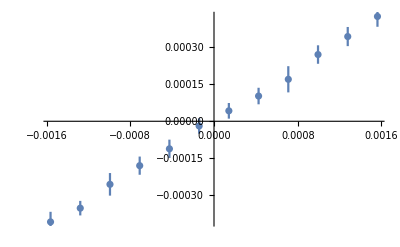

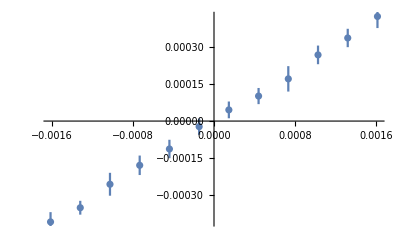

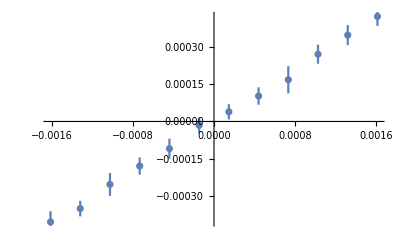

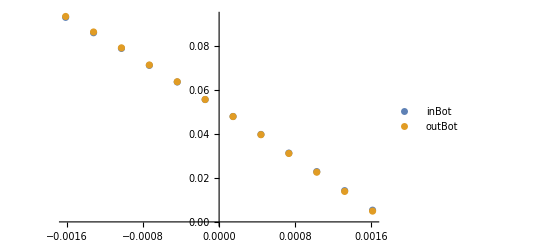

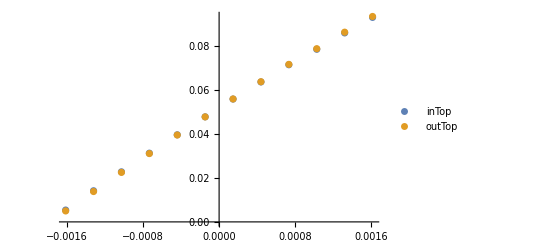

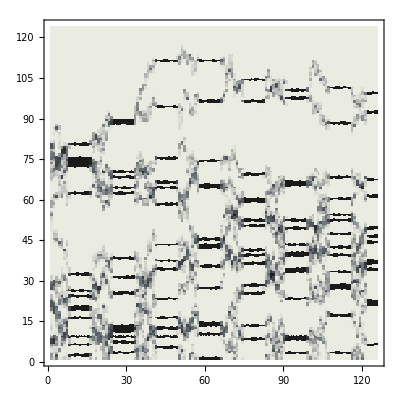

```mathematica
Needs["ErrorBarPlots`"];
location = "/Disk/ds-sopa-personal/s1373240/research/steadyStateFlow/ballRuns/attempt6/0/7/";
totFlowData = Import[location<>"mathFormatData.dat", "Data"];
ErrorListPlot[totFlowData]
topFlowData = Import[location<>"topFlowData.dat", "Data"];
ErrorListPlot[topFlowData]
botFlowData = Import[location<>"botFlowData.dat", "Data"];
ErrorListPlot[botFlowData]
inBotData = Import[location<>"inBotData.dat", "Data"];
outBotData = Import[location<>"outBotData.dat", "Data"];
ErrorListPlot[{inBotData, outBotData}, PlotLegends->{"inBot", "outBot"}]
inTopData = Import[location<>"inTopData.dat", "Data"];
outTopData = Import[location<>"outTopData.dat", "Data"];
ErrorListPlot[{inTopData, outTopData}, PlotLegends->{"inTop", "outTop"}]
trajData = Import[location<>"11/typeStats.dat", "Data"];
ListDensityPlot[trajData, InterpolationOrder->0, ColorFunction->"GrayTones", PlotRange->{0,1}]
```